/u/puchhamf/misc/workspace/ssj/data

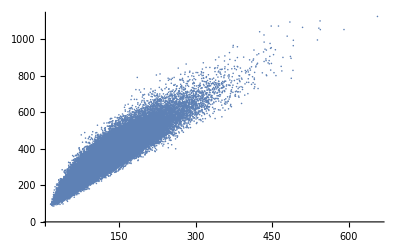

-Graphics3D-

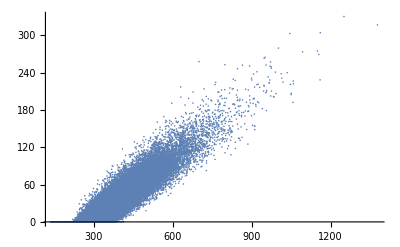

```mathematica
SetDirectory[NotebookDirectory[]]
dataRaw =Import["asian/MCData_Step_2.csv"];
n = 2^17;
data = RandomSample[dataRaw,n];
ListPlot[Table[{data[[i,1]],data[[i,2]]},{i,1,n}],PlotRange->All]
ListPointPlot3D[data,AxesLabel->{"S1","S2","Perf"},PlotRange->All]
fit = LinearModelFit[Table[{data[[i,1]],data[[i,2]]},{i,1,n}],x,x];
ListPlot[Table[{fit[data[[i,1]]],data[[i,3]]},{i,1,n}],PlotRange->All]
```

```mathematica
SetDirectory[NotebookDirectory[]];
dataRaw1=Import["ReversibleIsometrization/MCData_Step_4.csv"];
dataRaw2=Import["ReversibleIsometrization/SobData_Step_4.csv"];
n = 2^17;
data1 = RandomSample[dataRaw,n];
ListPlot[Table[{data[[i,1]],data[[i,2]]},{i,1,n}],PlotRange->All]
ListPointPlot3D[data,AxesLabel->{"S1","S2","Perf"},PlotRange->All]
fit = LinearModelFit[Table[{data[[i,1]],data[[i,2]]},{i,1,n}],x,x];
plot1 = ListPlot[Table[{fit[data[[i,1]]],data[[i,3]]},{i,1,n}],PlotRange->All];
```

-Graphics-

```mathematica
-Graphics-2^17
```

```mathematica
-Graphics-->
```